```mathematica
λL[k_,ν_]=(k ν)/((1+ν)(1-2ν));
μL[k_,ν_]=k/(2(1+ν));
LameCoefficients[κ_,ν_]={λ[k,ν], μ[k,ν]};
```

```mathematica
$Assumptions=_∈Reals;
Id= IdentityMatrix[2];
VenantKirchhoffPotential[F_,λ_,μ_]:=Module[{E},
E=1/2(Fᵀ.F-Id);
μ Tr[E.E]+λ/2 Tr[E]^2
]
NeoHookeanPotential[F_,λ_,μ_]:=Module[{E},
μ /2(Tr[Fᵀ.F]-2)-μ Log[Det[F]]+λ/2 Log[Det[F]]^2
]
NeoHookeanStress[F_,λ_,μ_]:=Module[{E},
μ(F-Inverse[F]ᵀ)+λ Log[Det[F]] Inverse[F]ᵀ
]
NeoHookeanStressDifferential[F_,dF_,λ_,μ_]:=Module[{E},
μ dF+(μ-λ Log[Det[F]])Inverse[F]ᵀ.dFᵀ.Inverse[F]ᵀ+λ Tr[(Inverse[F].dF)ᵀ] Inverse[F]ᵀ
]
VenantKirchhoffStress[F_,λ_,μ_]:=Module[{E},
E=1/2(Fᵀ.F-Id);
F.(2 μ E+λ Tr[E] Id)
]
VenantKirchhoffStressDifferential[F_,dF_,λ_,μ_]:=Module[{E,dE},
E=1/2(Fᵀ.F-Id);dE=1/2(dFᵀ.F+Fᵀ.dF);
dF.(2 μ E+λ Tr[E] Id)+F.(2 μ dE+λ Tr[dE] Id)
]
Ds[tr_]:=Transpose[tr[[1;;2]]-{tr[[3]],tr[[3]]}];
Bm[tr_]:=Inverse[Ds[tr]]

ElasticForce[P_,vA_]:=Module[{H},
H=-Abs[Det[Ds[vA]]]/2P.(Inverse[Ds[vA]])ᵀ;
{Hᵀ[[1]],Hᵀ[[2]],-Hᵀ[[1]]-Hᵀ[[2]]}
]

F[vA_,vB_]:=Ds[vB].Bm[vA];
ScanLine[α_,v_,vA_,k_,ν_]:=Module[{P,f},
f=ElasticForce[VenantKirchhoffStress[F[vA,v],k,ν],vA];
P=VenantKirchhoffStress[F[vA,v+α f],k,ν];
{-Flatten[ElasticForce[P,vA]].Flatten[f],
VenantKirchhoffPotential[F[vA,v+α f],k,ν],f}
]
W[x_]:=Area[Simplex[x]];

StressHessian[potential_,XX_,xx_,μ_,λ_]:=Module[{xT,XT},
xT=Table[x[2i+j],{i,0,2},{j,1,2}];
XT=Table[X[2i+j],{i,0,2},{j,1,2}];
-W[XT]Table[D[potential[F[XT,xT],μ,λ],x[i],x[j]],{i,1,6},{j,1,6}]/.{x[i_]-> Flatten[xx][[i]],X[i_]->  Flatten[XX][[i]]}
];
StressGradient[potential_,XX_,xx_,μ_,λ_]:=Module[{xT,XT},
xT=Table[x[2i+j],{i,0,2},{j,1,2}];
XT=Table[X[2i+j],{i,0,2},{j,1,2}];
-W[XT]Table[D[potential[F[XT,xT],μ,λ],x[i]],{i,1,6}]/.{x[i_]-> Flatten[xx][[i]],X[i_]->  Flatten[XX][[i]]}
];
MatrixComponents[A_]:=Table[UnitVector[6,i].A[UnitVector[6,j]],{i,1,6},{j,1,6}];
```

```mathematica
vA={{0,0},{0,1},{1,0}};
vB={{0,-1},{2,2},{1,-1}};
vInit = vA+0.7{{0,1},{0,0},{0,0}};
t1=10;
m1=StressHessian[NeoHookeanPotential,vA,vInit,1,1];
m2=MatrixComponents[
Flatten[ElasticForce[
NeoHookeanStressDifferential[F[vA,vInit],F[vA,Partition[#,2]],1,1],vA
]]&
];
Chop[m1-m2]//MatrixForm
g1=StressGradient[NeoHookeanPotential,vA,vInit,1,1];
g2=Flatten[ElasticForce[NeoHookeanStress[F[vA,vInit],1,1],vA]];
Chop[g1-g2]
```

(0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0)

{0,0,0,0,0,0}

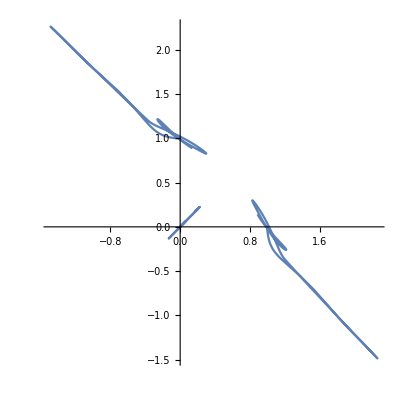

```mathematica
ElasticTriangleSimulation[vertices_, externalForce_,P_,dP_,t1_,kDamp_:0.3]:=Module[{state, rhs, lhs},
state[t_]=Table[i[j][t],{j,1,3},{i,{xc,yc}}];
rhs=ElasticForce[P[F[vertices,state[t]]],vertices]+
     kDamp  ElasticForce[dP[F[vertices,state[t]],F[vertices,state'[t]]],vertices]+
externalForce[t];
lhs=state''[t];
state[t]/.NDSolve[{lhs==rhs,
state[0]==vertices,state'[0]==0vertices},state[t],{t,0,t1},Method->"Adams"][[1]]
]

fExt[t_]=2{{1,1},{-1,0},{0,-1}}HeavisideTheta[5-t];
vertices[t_]=ElasticTriangleSimulation[vA, fExt,NeoHookeanStress[#,1,1]&,
NeoHookeanStressDifferential[#1,#2,1,1]&,t1,.1];
ParametricPlot[vertices[t],{t,0,t1}]
Animate[
Graphics[Triangle[vertices[t]],Axes->True,PlotRange->{{-2,2},{-2,2}}]
,{t,0,t1}]
```

```mathematica
Plot[Det[F[vA, system[t]/.sol[t][[1]]]],{t,0,t1},PlotRange->Full]
```

-Graphics-

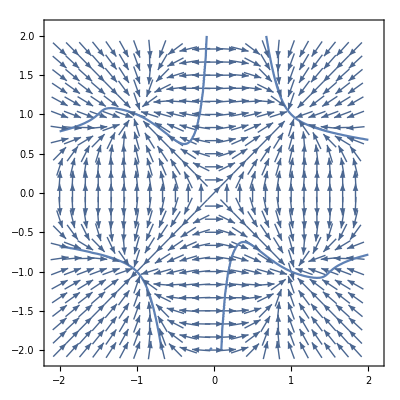

{1/8 (4 sx (-2+sx^2+sy^2) λ+2 (-4 sx+4 sx^3) μ),1/8 (4 sy (-2+sx^2+sy^2) λ+2 (-4 sy+4 sy^3) μ)}

1/8 (4 sy (-2+sx^2+sy^2)+2 (-4 sy+4 sy^3))+((2 (-4 sx+4 sx^3)+4 sx (-2+sx^2+sy^2)) (4 (sx-sy) (sx+sy)+√(16 sx^4-28 sx^2 sy^2+16 sy^4)))/(16 sx sy)

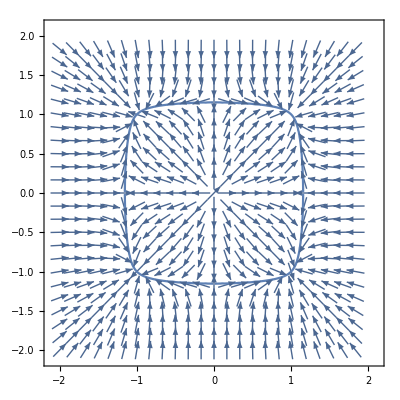

```mathematica
FSVD = ({{Cos[ϕ], -Sin[ϕ]}, {Sin[ϕ], Cos[ϕ]}}).({{sx, 0}, {0, sy}}).({{Cos[θ], -Sin[θ]}, {Sin[θ], Cos[θ]}});
ψv[sx_,sy_]=FullSimplify[NeoHookeanPotential[FSVD,λ,μ]];<<<
vf=-D[ψv[sx,sy],{{sx,sy}}]/.{μ->1,λ->1};
vp=VectorPlot[Re[vf],{sx,-2,2},{sy,-2,2},VectorScale->{Automatic,Automatic,None},VectorStyle->Tiny,
VectorPoints->Fine];
grad=D[ψv[sx,sy],{{sx, sy}}];
Hess=FullSimplify[D[grad,{{sx,sy}}]];
temp=FullSimplify[Eigensystem[Hess]];
Simplify[temp[[1,1]]-temp[[1,2]]];
eigenv=temp[[2,2]];
cont = Re[(grad.eigenv)]/.{μ->1,λ->1};
Show[{vp,ContourPlot[cont==0,{sx,-2,2},{sy,-2,2}]}]
```

1/8 (4 sy (-2+sx^2+sy^2)+2 (-4 sy+4 sy^3))+((2 (-4 sx+4 sx^3)+4 sx (-2+sx^2+sy^2)) (4 (sx-sy) (sx+sy)+√(16 sx^4-28 sx^2 sy^2+16 sy^4)))/(16 sx sy)

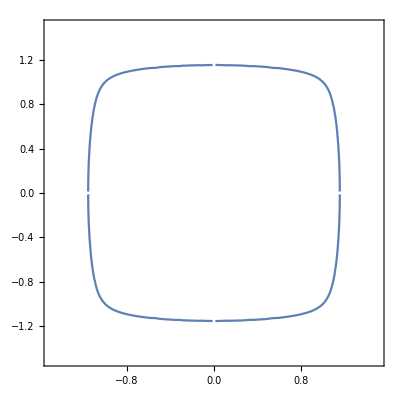

```mathematica
cont=(grad.eigenv)/.{μ->1,λ->1}
ContourPlot[cont==0,{sx,-1.5,1.5},{sy,-1.5,1.5}]
```